## Basic usage and computing A,B.

Here is a notebook that explains how to interact with the data (JSON files) generated by the ocaml program.

The directory structure of the repository where this file is located looks like

adam@adam-ThinkPad-T580:~/src/gits/BIL-numerical-T2$ tree -d -L 1 -I “_build|_opam” ./
./
├── initial_data
├── long_runs
├── test
└── utilities

4 directories

This file is in the utilities directory, and you should open it by double clicking there. When you open it, by default, paths are relative to your home directory. The following command sets paths to be relative to the directory where this file (t2_data.nb) is located. Click anywhere in the following cell and evaluate the cell to make the change. (On my machine, I type shift+enter to evaluate a cell.)

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/adam/src/gits/BIL-numerical-T2/utilities

If you evaluated it correctly, the output should be the full path to the directory where t2_data.nb is located.

The json data are located in “../long_runs”. We can list the contents of that directory with the following command. The output of this command is long, so we only return the first four elements by feeding the output of the FileNames function into the Take function.

```mathematica
FileNames["*","../long_runs"]//Take[#,4]&
```

{../long_runs/stop,../long_runs/t_b0_0_1024.1.json,../long_runs/t_b0_0_1024.json,../long_runs/t_b0_0_2048.1.json}

Here is a simpler example to make the role of the // operator more clear:

```mathematica
{1,2,3,4,5,6,7,8,9,10}//Take[#,7]&
```

{1,2,3,4,5,6,7}

This is exactly the same as evaluating

```mathematica
Take[{1,2,3,4,5,6,7,8,9,10},7]
```

{1,2,3,4,5,6,7}

Let’s see what we get when we import one of these json files:

```mathematica
Import["../long_runs/t_b0_0_512.1.json"]
```

{initial time→0.,5,evolution→{{time→0.,data→{1}},507,{time→20.999,data→{{-17.472,-17.472,508,-17.472,-17.472},4,{1}}}}}
 |  |  |  |

This takes quite some time, and returns a list that has the form { name1 -> value1 , name2 -> value2 , ... }. It’s better to assign this to a name so we can manipulate it more easily.

```mathematica
exampleimport =Import["../long_runs/t_b0_0_512.1.json"];
```

The semicolon at the end of the above line suppresses anything from being printed in the output cell.

Let’s look at this thing called exampleimport.

```mathematica
exampleimport//Head
```

List

exampleimport has type List

```mathematica
exampleimport//Length
```

7

the list is 7 elements long

```mathematica
exampleimport[[1]]
```

initial time→0.

this is the first element

```mathematica
exampleimport//Map[First]
```

{initial time,fourier coefficients,time limit,checkpoint size,resolution,print frequency,evolution}

Map[...] applies some function to every element of a list. In this case the function that we apply is First. This is just just returns the first element of an object. Since each element in exampleimport has the form nameN -> valueN, First[nameN -> valueN] just returns nameN.

For plotting, we only need the part “evolution”. We could pick this out using

```mathematica
exampleimport[[7,2]]
```

{{time→0.,data→{{0.951703,0.963582,0.975029,0.986036,0.996596,502,0.886129,0.900038,0.913559,0.926683,0.939401},4,{1}}},507,1}
 |  |  |  |

That is, take the 7th part of exampleimport, then take the 2nd part of that.

An easier way to do it is

```mathematica
exampleevolution="evolution"/.exampleimport
```

{{time→0.,data→{{0.951703,0.963582,0.975029,0.986036,0.996596,502,0.886129,0.900038,0.913559,0.926683,0.939401},4,{1}}},507,1}
 |  |  |  |

If we cared to, we could also get other information from exampleimport

```mathematica
"resolution"/.exampleimport
```

512

The thing we have assigned to the name exampleevolution is also a list:

```mathematica
exampleevolution//Head
```

List

Each of its elements has the following form:

```mathematica
exampleevolution//First//ToString//StringTake[#,1000]&
```

{time -> 0., data -> {{0.951703, 0.963582, 0.975029, 0.986036, 0.996596, 1.0067, 1.01634, 1.02552, 1.03422, 1.04244, 1.05017, 1.05741, 1.06416, 1.0704, 1.07615, 1.08138, 1.0861, 1.09031, 1.094, 1.09717, 1.09982, 1.10194, 1.10355, 1.10463, 1.10518, 1.10521, 1.10472, 1.1037, 1.10216, 1.1001, 1.09753, 1.09444, 1.09083, 1.08672, 1.08209, 1.07697, 1.07135, 1.06523, 1.05863, 1.05154, 1.04398, 1.03594, 1.02744, 1.01848, 1.00907, 0.999219, 0.98893, 0.978212, 0.967076, 0.955528, 0.94358, 0.931238, 0.918515, 0.905418, 0.89196, 0.878149, 0.863997, 0.849515, 0.834715, 0.819607, 0.804203, 0.788516, 0.772559, 0.756342, 0.73988, 0.723184, 0.706269, 0.689147, 0.671832, 0.654337, 0.636677, 0.618865, 0.600916, 0.582843, 0.564661, 0.546385, 0.528029, 0.509607, 0.491136, 0.472628, 0.454101, 0.435567, 0.417044, 0.398544, 0.380085, 0.361681, 0.343346, 0.325097, 0.306948, 0.288915, 0.271013, 0.253256, 0.235661, 0.218241, 0.201012, 0.183988, 0.167185, 0.150617, 0.134298, 0.118244, 0.102468, 0.0869849, 0.07180

We used //ToString//StringTake[#,1000]& to truncate the long output.

Let’s finally look at the information contained in the “data” field.

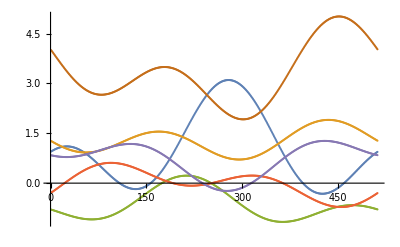

```mathematica
exampleevolution//First//"data"/.#&//ListPlot
```

exampleevolution is a list of what we might call “timeframes”; objects of the form { “time” -> ... , “data” -> { ... } }

exampleevolution//First is the first timeframe that we printed above: {time -> 0., data -> {{0.951703, 0.96 .... }} }

exampleevolution//First//”data”/.#& is the data part of the first timeframe. It is a list of length 6. Each element is a list of floats that encodes the function values in the order { p , pi_p , q , pi_q , lambda , pi_lambda }. The plot above is then these 6 functions.

One might wonder why I should include a field labeled “time”. Recall that Δt is not the same throughout the run.

This is rather convoluted, so we can shorthand this process. We define the function

```mathematica
p[timeframe_]:=("data"/.timeframe)[[1]]
```

which takes a timeframe, gets its data component, and takes the first element of the data component, which we know is the function p.

Then we can write simply

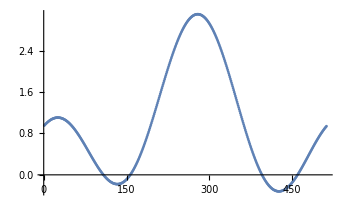

```mathematica
exampleevolution//First//p//ListPlot
```

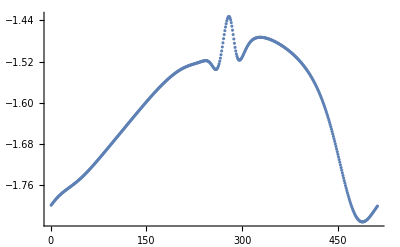

```mathematica
exampleevolution[[100]]//p//ListPlot
```

Since exampleevolution is a list of timeframes, we can define a function which takes a timeframe as an input

```mathematica
τ[timeframe_]:=("time"/.timeframe)
point[timeframe_]:={ τ[timeframe] , Mean[p[timeframe]] } (* x is the time of the timeframe, y is the mean of P over that timeframe. *)
```

and map that function over the list exampleevolution.

```mathematica
exampleevolution//Map[point]//ToString//StringTake[#,1000]&
```

{{0., 0.982405}, {0.051056, 0.96661}, {0.114923, 0.938368}, {0.180396, 0.905273}, {0.244703, 0.870449}, {0.307382, 0.834967}, {0.36816, 0.799452}, {0.426895, 0.764299}, {0.483532, 0.729761}, {0.538075, 0.696}, {0.590568, 0.663114}, {0.641079, 0.631156}, {0.689687, 0.600152}, {0.736481, 0.570104}, {0.781553, 0.541}, {0.824993, 0.512821}, {0.866891, 0.48554}, {0.90733, 0.459127}, {0.965431, 0.421064}, {1.02069, 0.38477}, {1.07334, 0.350135}, {1.12358, 0.317052}, {1.17162, 0.285422}, {1.21761, 0.255151}, {1.26171, 0.226152}, {1.30407, 0.198346}, {1.34481, 0.171658}, {1.39679, 0.1377}, {1.44632, 0.105464}, {1.49362, 0.074823}, {1.53887, 0.0456586}, {1.58222, 0.0178668}, {1.62384, -0.00864637}, {1.66385, -0.0339655}, {1.71177, -0.0640507}, {1.75756, -0.0925223}, {1.8014, -0.119498}, {1.84343, -0.145084}, {1.88381, -0.169374}, {1.93024, -0.196927}, {1.97465, -0.222864}, {2.01721, -0.247299}, {2.05805, -0.270333}, {2.10372, -0.29556}, {2.14742, -0.319136}, {2.18931, -0.341177}, {2.22954, -0.3

Again, the output is long so we truncate it. We can plot these (x,y) pairs.

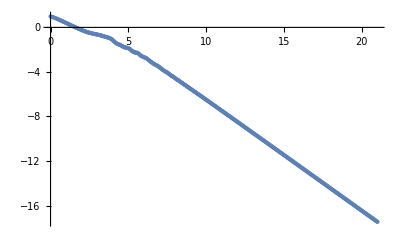

```mathematica
exampleevolution//Map[point]//ListPlot
```

Okay, now we know how to take a file and get a list of timeframes from it. And we know how to define a function that acts on timeframes and evaluate it on the timeframes stored in that file. Evaluate the next cell to define a bunch of functions which act on timeframes. We already defined the functions p and τ above, but we can redefine them here without hurting anything.

```mathematica
(* Functions one can calculate on each time frame. *)
p[timeframe_]:=("data"/.timeframe)[[1]]
πp[timeframe_]:=("data"/.timeframe)[[2]]
q[timeframe_]:=("data"/.timeframe)[[3]]
πq[timeframe_]:=("data"/.timeframe)[[4]]
λ[timeframe_]:=("data"/.timeframe)[[5]]
πλ[timeframe_]:=("data"/.timeframe)[[6]]
τ[timeframe_]:=("time"/.timeframe)
α[timeframe_]:=1/(2πλ[timeframe])^2
v[timeframe_]:=p[timeframe]+τ[timeframe]
ρ[timeframe_]:=-1/2 Log[α[timeframe]]
l[timeframe_]:=p[timeframe]+1/2λ[timeframe]-3/2τ[timeframe]-Log[2]
Ptau[timeframe_]:=-πp[timeframe]/(2*πλ[timeframe])
Qtau[timeframe_]:=-Exp[-2p[timeframe]]πq[timeframe]/(2*πλ[timeframe])
Vtau[timeframe_]:=Ptau[timeframe]+1
ρtau[timeframe_]:=Exp[l[timeframe]]
ltau[tf_]:=-2-ρtau[tf]+1/2En[tf]
A[timeframe_]:=Mean[-πp[timeframe]+2πλ[timeframe]+q[timeframe]*πq[timeframe]];
B[timeframe_]:=Mean[-πq[timeframe]];
c[tf_]:=Mean[(Qtau[tf]-2q[tf]+q[tf]Vtau[tf])2 πλ[tf]+q[tf](-πp[tf]+2πλ[tf]+q[tf]*πq[tf])];
```

Note that we defined how to calculate A and B from a timeframe here.

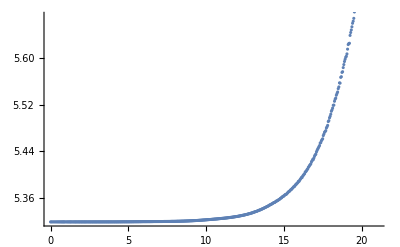

```mathematica
point[timeframe_]:={τ[timeframe],A[timeframe]}
exampleevolution//Map[point]//ListPlot
```

This doesn't look very constant, but remember that we’re looking at a low resolution run, and if you look at the scale on the left it makes the situation seem less bad.

Okay, now what is the process of going from a file to the value of A? Let’s go back and look at the output of FileNames[“*”,”../long_runs”] again.

```mathematica
FileNames["*","../long_runs"]//Take[#,20]&//TableForm
```

../long_runs/stop
../long_runs/t_b0_0_1024.1.json
../long_runs/t_b0_0_1024.json
../long_runs/t_b0_0_2048.1.json
../long_runs/t_b0_0_2048.json
../long_runs/t_b0_0_4096.1.json
../long_runs/t_b0_0_4096.json
../long_runs/t_b0_0_512.1.json
../long_runs/t_b0_0_512.json
../long_runs/t_b0_121_1024.1.json
../long_runs/t_b0_121_1024.json
../long_runs/t_b0_121_2048.1.json
../long_runs/t_b0_121_2048.json
../long_runs/t_b0_121_4096.1.json
../long_runs/t_b0_121_4096.json
../long_runs/t_b0_121_512.1.json
../long_runs/t_b0_121_512.json
../long_runs/t_b0_13_1024.1.json
../long_runs/t_b0_13_1024.json
../long_runs/t_b0_13_2048.1.json

What are all these files? t_ is just a prefix for the data output by the simulation program. The next part is either b0_, pol_, or gen_ depending on whether the initial data is B_0, polarised, or generic. The next number is between 0 and 199 inclusive and is just the label of the run. The next field is either 512, 1024, 2048, or 4096 and indicates the spatial resolution. But why are there two “t_b0 _ 0_ 1024” files? That is, t_b0_0_1024.json and t_b0_0_1024.1.json. If we import the first one, we can see what is going on:

```mathematica
"evolution"/.Import["../long_runs/t_b0_0_1024.json"]//Length
```

1

So the file t_b0_0_1024.json only has one timeframe in its “evolution” field. This is the data at the initial time, which has been generated from the Fourier coefficients. When the OCaml program runs, it reads this file and uses the initial data to start the simulation. When it outputs data, however, it writes files t_b0_0_1024.1.json, t_b0_0_1024.2.json et cetera until it reaches the specified final time.

Okay, if we want to calculate A for every piece of initial data, then we only need the initial data file, not the full evolution files *.1.json , *.2.json and so on. So let’s get a list of just these initial data files.

```mathematica
FileNames["*","../long_runs"]//Select[Not[StringMatchQ[#,"*.1.json"]||StringMatchQ[#,"*.2.json"]]&]//Take[#,20]&//TableForm
```

../long_runs/stop
../long_runs/t_b0_0_1024.json
../long_runs/t_b0_0_2048.json
../long_runs/t_b0_0_4096.json
../long_runs/t_b0_0_512.json
../long_runs/t_b0_121_1024.json
../long_runs/t_b0_121_2048.json
../long_runs/t_b0_121_4096.json
../long_runs/t_b0_121_512.json
../long_runs/t_b0_13_1024.json
../long_runs/t_b0_13_2048.json
../long_runs/t_b0_13_4096.json
../long_runs/t_b0_13_512.json
../long_runs/t_b0_139_1024.json
../long_runs/t_b0_139_2048.json
../long_runs/t_b0_139_4096.json
../long_runs/t_b0_139_512.json
../long_runs/t_b0_162_1024.json
../long_runs/t_b0_162_2048.json
../long_runs/t_b0_162_4096.json

Note that we still get 4 initial data files for each piece of initial data: one for each of the four resolutions. To calculate A, though, we only need one of these. So let’s just select the 512 resolution ones.

```mathematica
FileNames["*_512.json","../long_runs"]//Take[#,20]&//TableForm
```

../long_runs/t_b0_0_512.json
../long_runs/t_b0_121_512.json
../long_runs/t_b0_13_512.json
../long_runs/t_b0_139_512.json
../long_runs/t_b0_162_512.json
../long_runs/t_b0_172_512.json
../long_runs/t_b0_179_512.json
../long_runs/t_b0_180_512.json
../long_runs/t_b0_190_512.json
../long_runs/t_b0_24_512.json
../long_runs/t_b0_26_512.json
../long_runs/t_b0_43_512.json
../long_runs/t_b0_58_512.json
../long_runs/t_b0_61_512.json
../long_runs/t_b0_64_512.json
../long_runs/t_b0_81_512.json
../long_runs/t_b0_85_512.json
../long_runs/t_b0_89_512.json
../long_runs/t_b0_9_512.json
../long_runs/t_gen_0_512.json

Okay, now that we have the files we want to act on, let’s write a function that takes a file and produces the triple { filename , A , B }.

```mathematica
f[filename_]:=Module[{import,evo,firstframe}, (* wrapping this in a Module box ensures that import, evo, and firstframe have local scope. *)
import=Import[filename];
evo="evolution"/.import;
firstframe=evo//First;
{filename, A[firstframe],B[firstframe]}
]
f["../long_runs/t_b0_9_512.json"]
```

{../long_runs/t_b0_9_512.json,3.16677,-1.73472×10^-18}

Now we can map this function over all the files produced by FileNames[“*_512.json”,”../long_runs”] to get them packed into a nice list.

```mathematica
abdata=FileNames["*_512.json","../long_runs"]//Map[f]
```

{{../long_runs/t_b0_0_512.json,5.31887,-2.68882×10^-17},{../long_runs/t_b0_121_512.json,3.35561,1.43657×10^-18},{../long_runs/t_b0_13_512.json,9.08415,2.42861×10^-17},{../long_runs/t_b0_139_512.json,9.08684,2.10877×10^-17},{../long_runs/t_b0_162_512.json,4.54853,-3.51282×10^-17},{../long_runs/t_b0_172_512.json,4.72947,-2.86229×10^-17},{../long_runs/t_b0_179_512.json,1.78583,5.0822×10^-19},{../long_runs/t_b0_180_512.json,-11.5762,-7.97973×10^-17},{../long_runs/t_b0_190_512.json,1.00831,3.84892×10^-18},{../long_runs/t_b0_24_512.json,14.2229,-1.24033×10^-16},{../long_runs/t_b0_26_512.json,0.523264,-2.34188×10^-17},{../long_runs/t_b0_43_512.json,1.75625,-1.40946×10^-17},{../long_runs/t_b0_58_512.json,4.56765,1.05168×10^-17},{../long_runs/t_b0_61_512.json,10.3372,3.15503×10^-17},{../long_runs/t_b0_64_512.json,6.11423,1.6263×10^-17},{../long_runs/t_b0_81_512.json,7.82669,3.13741×10^-18},{../long_runs/t_b0_85_512.json,7.58898,2.20229×10^-18},{../long_runs/t_b0_89_512.json,1.09303,-6.1149×10^-17},{../long_runs/t_b0_9_512.json,3.16677,-1.73472×10^-18},{../long_runs/t_gen_0_512.json,4.41178,-0.978214},{../long_runs/t_gen_121_512.json,3.28582,0.239005},{../long_runs/t_gen_13_512.json,8.7913,-0.126832},{../long_runs/t_gen_139_512.json,8.51905,0.344777},{../long_runs/t_gen_156_512.json,1.68018,0.957317},{../long_runs/t_gen_162_512.json,4.30096,-0.924357},{../long_runs/t_gen_163_512.json,-2.30351,0.3552},{../long_runs/t_gen_172_512.json,5.02524,0.408361},{../long_runs/t_gen_179_512.json,1.38711,0.810813},{../long_runs/t_gen_190_512.json,4.02756,0.914832},{../long_runs/t_gen_192_512.json,2.60474,0.539019},{../long_runs/t_gen_24_512.json,5.00432,0.897163},{../long_runs/t_gen_43_512.json,2.15162,0.211017},{../long_runs/t_gen_58_512.json,3.60469,0.748498},{../long_runs/t_gen_61_512.json,11.8741,-0.724321},{../long_runs/t_gen_64_512.json,6.03403,0.0421757},{../long_runs/t_gen_69_512.json,2.60493,-0.484623},{../long_runs/t_gen_81_512.json,9.337,-0.425272},{../long_runs/t_gen_85_512.json,8.06716,-0.90557},{../long_runs/t_gen_90_512.json,1.97636,0.40878},{../long_runs/t_gen_9_512.json,2.46403,-0.705462},{../long_runs/t_pol_104_512.json,5.71051,0.},{../long_runs/t_pol_105_512.json,8.37147,0.},{../long_runs/t_pol_107_512.json,7.6022,0.},{../long_runs/t_pol_108_512.json,4.37429,0.},{../long_runs/t_pol_113_512.json,6.46319,0.},{../long_runs/t_pol_124_512.json,15.8985,0.},{../long_runs/t_pol_131_512.json,23.6665,0.},{../long_runs/t_pol_144_512.json,6.23928,0.},{../long_runs/t_pol_151_512.json,7.9945,0.},{../long_runs/t_pol_164_512.json,7.41415,0.},{../long_runs/t_pol_167_512.json,8.98571,0.},{../long_runs/t_pol_168_512.json,-15.0374,0.},{../long_runs/t_pol_186_512.json,0.000113536,0.},{../long_runs/t_pol_193_512.json,2.24356,0.},{../long_runs/t_pol_196_512.json,2.46365,0.},{../long_runs/t_pol_197_512.json,11.5672,0.},{../long_runs/t_pol_3_512.json,5.47366,0.},{../long_runs/t_pol_90_512.json,3.06358,0.}}

It’s then possible to export this as a tsv if we want. Since abdata is a list of lists, exporting to a tsv puts each element eg {../long_runs/t_pol_105_512.json,8.37147,0.} on its own line.

```mathematica
Export["abdata.tsv",abdata]
```

abdata.tsv

This file appears in the working directory, which we set at the first line of the notebook to be the notebook directory (where t2_data.nb is located).

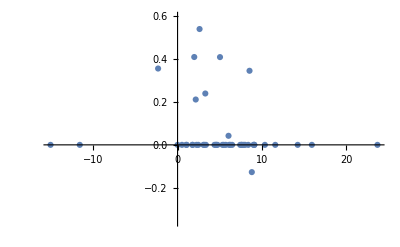

```mathematica
f[filename_]:=Module[{import,evo,firstframe}, (* wrapping this in a Module box ensures that import, evo, and firstframe have local scope. *)
import=Import[filename];
evo="evolution"/.import;
firstframe=evo//First;
{ A[firstframe],B[firstframe]}
]
FileNames["*_512.json","../long_runs"]//Map[f]//ListPlot
```

## Advanced usage and computing arbitrary functions along a run.

Now that we can read a file and compute functions from the data in that file, let’s look at some more examples.

First, in addition to the functions acting on time frames above, we might want to compute functions involving spatial derivatives. To that end we define

```mathematica
(* Computes a finite-difference spatial derivative of a function on a time frame. *)
spacederivative[f_,tf_]:=Module[{temp,n,Δx},
temp=f[tf];
n=Length[temp];
Δx=2 Pi / n;
temp=Join[
{temp[[n-1]]},
{temp[[n]]},
temp,
{temp[[1]]},
{temp[[2]]}
];
Table[(2/3*(temp[[i+1]]-temp[[i-1]])+1/12*(temp[[i-2]]-temp[[i+2]]))/Δx,{i,1+2,n+2}]
]
```

This allows us to give the definition of λtau, the constraint, and some other things

```mathematica
λtau[tf_]:=1/(2*πλ[tf])^2(
πp[tf]^2+Exp[-2p[tf]]πq[tf]^2+Exp[-2τ[tf]]spacederivative[p,tf]^2+Exp[2(p[tf]-τ[tf])]spacederivative[q,tf]^2
)+Exp[(λ[tf]+2p[tf]+3τ[tf])/2]

(* Calculate the constraint. Note that this is pointwise in space. This should be identically 0 for solutions without error. *)
galconstraint[tf_]:=Module[{dp,dq,dλ},
 dp=spacederivative[p,tf];
 dq=spacederivative[q,tf];
 dλ=spacederivative[λ,tf];
(dp*πp[tf])+(dq*πq[tf])+(dλ*πλ[tf])
]
galconstraintavg[tf_]:=Mean[galconstraint[tf]]

(* More functions that can be computed on time frames. *)
Ev[tf_]:=Vtau[tf]^2+Exp[2(τ[tf]-ρ[tf])]spacederivative[p,tf]^2
Eq[tf_]:=Exp[2(v[tf]-τ[tf])](Qtau[tf]^2+Exp[2(τ[tf]-ρ[tf])]spacederivative[q,tf]^2)
En[tf_]:=Ev[tf]+Eq[tf]
J[tf_]:=1/2 En[tf]
mE[tf_]:=Mean[Exp[ρ[tf]-2τ[tf]] J[tf]]
Π[tf_]:=Mean[Exp[ρ[tf]] ]
Λ[tf_]:=1/2Mean[Exp[-2τ[tf]+ρ[tf]]Vtau[tf](v[tf]-Mean[v[tf]]-1)]
H[tf_]:=Π[tf](mE[tf]+Λ[tf])
Y[tf_]:=Mean[Exp[l[tf]+ρ[tf]+2τ[tf]]]
cc[tf_]:=Π[tf]Exp[-τ[tf]]H[tf]^(-1/2)
dd[tf_]:=Y[tf]Exp[-3τ[tf]]H[tf]^(-1/2)

(* The terms from Beverly's superhamiltonian. The 'a' versions below just have an extra factor of 1/πλ so that they are O(1) generically. *)
H0[timeframe_]:=πp[timeframe]*πp[timeframe]/(4*πλ[timeframe])
Hkin[tf_]:=Exp[-2 p[tf]] πq[tf]*πq[tf]/(4*πλ[tf])
Hsmall[tf_]:=Exp[2 τ[tf]] spacederivative[p,tf]*spacederivative[p,tf]/(4*πλ[tf])
Hcurv[tf_]:=Exp[2 τ[tf]]Exp[2 p[tf]]spacederivative[q,tf]*spacederivative[q,tf]/(4*πλ[tf])
Htwist[tf_]:=πλ[tf] Exp[-3τ[tf]/2]Exp[λ[tf]/2+p[tf]]

H0a[timeframe_]:=πp[timeframe]*πp[timeframe]/(4*πλ[timeframe]*πλ[timeframe])
Hkina[tf_]:=Exp[-2 p[tf]] πq[tf]*πq[tf]/(4*πλ[tf]*πλ[tf])
Hsmalla[tf_]:=Exp[2 τ[tf]] spacederivative[p,tf]*spacederivative[p,tf]/(4*πλ[tf]*πλ[tf])
Hcurva[tf_]:=Exp[2 τ[tf]]Exp[2 p[tf]]spacederivative[q,tf]*spacederivative[q,tf]/(4*πλ[tf]*πλ[tf])
Htwista[tf_]:= Exp[-3τ[tf]/2]Exp[λ[tf]/2+p[tf]]
```

Unfortunately, at this point it is wise to define our own import function for JSON files. I discovered I needed at this at some point when I ran into the bug described here https://mathematica.stackexchange.com/questions/163825/problem-to-import-numbers-longer-than-19-digit-with-json-or-rawjson .

It isn’t necessary to understand this function. It operates just like Import but circumvents the error.

```mathematica
myimport[path_]:=Module[{text,timeframes},
Import[path,"Text"]//StringReplace[{"{"->"<|","}"->"|>",":"->"->","["->"{","]"->"}","e+"~~s_:>" 10^"~~s,"e-"~~s_:>" 10^-"~~s}]//ToExpression
]
```

At the end of the last section, we imported a bunch of files and applied a function to all of them. Let’s look at another example.

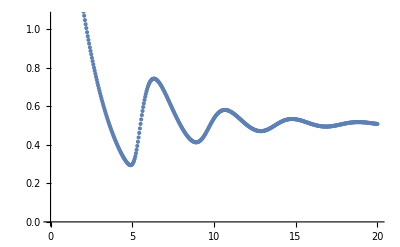

```mathematica
point[tf_]:={ τ[tf] , Exp[-τ[tf]/2]Mean[πλ[tf]] } 

Module[{evo,timeframes},
evo=myimport["../long_runs/t_b0_121_1024.1.json"];
timeframes="evolution"/.evo;
timeframes//Map[point]//ListPlot
]
```

We wrap the actual import and the computation of the data points in a Module so that Mathematica knows not to keep those in the memory once it is done outputting the plot. (Remember, Module tells Mathematica to make evo and timeframes local in scope.)

We might want to plot a lot of things repeatedly, with small changes, to it seems like a good idea to wrap the code above in a function. The function takes as input a filename and a function and returns a list of (x,y) pairs.

```mathematica
(* Returns a nice (x,y) table after applying the function f to all the time frames. *)
ClearAll[pairs];
pairs[file_,f_]:=Module[{evo,timeframes},
evo=file//myimport;
timeframes="evolution"/.evo;
Table[
{ τ[i] ,f[i] }
,{i,timeframes}]//Sort[#,#1[[1]]<#2[[1]]&]&
]
```

The last Sort command just sorts the (x,y) pairs by the value in the x place. Note that this function just returns a list of ordered pairs. We have to send the output to ListPlot to get a picture.

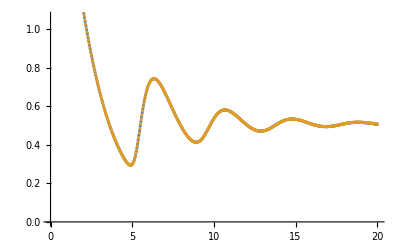

```mathematica
{
pairs["../long_runs/t_b0_121_512.1.json",Exp[-τ[#]/2]Mean[πλ[#]] &  ]
,pairs["../long_runs/t_b0_121_1024.1.json",Exp[-τ[#]/2]Mean[πλ[#]] &  ]
}//ListPlot
```

That works quite nicely, but it takes a long time to compute. Why? Because each time we run the pairs function, we read the entire JSON file from the disk which is slow. If you’re just working with one file for a while and creating many different plots, it makes sense to just import that file into the Mathematica session and plot what you need from there. But what if we want to plot across a lot of different files? It would make sense to save what we have already computed, and only reload the file if 1) the file has changed or 2) we’re computing something we haven’t previously computed. We can do this through memoization. Look at the following helper function:

```mathematica
ClearAll[pairshelper];
pairshelper[file_,f_,size_,date_]:=pairshelper[file,f,size,date]=Module[{evo,timeframes},
evo=file//myimport;
timeframes="evolution"/.evo;
Table[
{ τ[i] ,f[i] }
,{i,timeframes}]//Sort[#,#1[[1]]<#2[[1]]&]&
]


ClearAll[pairs];
pairs[file_,f_]:=pairshelper[file,f,file//FileByteCount,file//FileDate//UnixTime];
```

Now when we call the pairs function, it calculates the size and last modification time of the file we’re looking at and passes those four parameters to pairshelper. pairshelper computes the result in exactly the same way that our old pairs function did, but there is an extra bit before the Module invocation. This tells Mathematica to save the result of the computation, and if pairshelper is called with exactly the same arguments a second time, return the saved result and don’t read the file again.

Let’s try the computation we did above again:

```mathematica
AbsoluteTiming[{
pairs["../long_runs/t_b0_121_512.1.json",Exp[-τ[#]/2]Mean[πλ[#]] &  ]
,pairs["../long_runs/t_b0_121_1024.1.json",Exp[-τ[#]/2]Mean[πλ[#]] &  ]
}//ListPlot]
```

{21.6692,-Graphics-}

The first time we run it, it takes a few seconds because it has to read the two large JSON files. If we evaluate the same expression again, however

```mathematica
AbsoluteTiming[{
pairs["../long_runs/t_b0_121_512.1.json",Exp[-τ[#]/2]Mean[πλ[#]] &  ]
,pairs["../long_runs/t_b0_121_1024.1.json",Exp[-τ[#]/2]Mean[πλ[#]] &  ]
}//ListPlot]
```

{0.056304,-Graphics-}

It returns a result almost immediately. This is because the file has not changed and the function we’re evaluating on it has not changed either.

Before we move on, there are two modifications to the helper function we should make. It’s not necessary to understand these.

1) If the underlying file has changed, we should delete old memoized values.
2) If the data is split across multiple JSON files, we should read data from all the files.

```mathematica
ClearAll[pairshelper2];
pairshelper2[file_,f_,size_,date_]:=pairshelper2[file,f,size,date]=Module[{data,timeframes},
PrintTemporary[file];
pairshelper2//DownValues//Map[#[[1]]&]//Select[StringMatchQ[ToString[#],___~~file~~___]&]//Select[StringMatchQ[ToString[#],___~~ToString[f]~~___]&]//Map[(#=.)&]; (* Clear previous memoizations for this function and file if they exist. *)
data=file//myimport;
timeframes=("evolution"/.data);
Table[{τ[i],f[i]},{i,timeframes}]
]

ClearAll[pairshelper1];
pairshelper1[file_,f_]:=pairshelper2[file,f,file//FileByteCount,file//FileDate//UnixTime]

files[file_]:=Module[{root,dir,reses,filenames},
dir=DirectoryName[file];
root=FileBaseName[file];
FileNames[root<>".*.json",{dir}]
]

ClearAll[pairs];
pairs[file_,f_]:=Module[{fls,out},
fls=files[file]//Flatten;
out=Table[
j->pairshelper1[j,f]
,{j,fls}]//Flatten[#,1]&;
(files[file]/.out)//Flatten[#,1]&//SortBy[#[[1]]&]
]
```

The run t_gen_24_2048 has output data split across two files. Now pairs loads data from both before sorting the output.

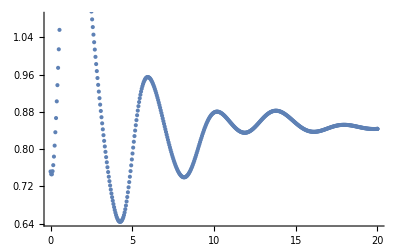

```mathematica
pairs["../long_runs/t_gen_24_2048.json",Exp[-τ[#]/2]Mean[πλ[#]] &  ]//ListPlot
```

```mathematica
pairs["../long_runs/t_b0_89_4096.json",Log10[Mean[Exp[ρ[#]]Vtau[#]]] & ]//MovingAverage[#,10]&//Re
```

{{0.189495,-0.160441},{0.231801,-0.14287},{0.273956,-0.124021},{0.316234,-0.103918},{0.358887,-0.0825881},{0.40184,-0.0602459},{0.444535,-0.0373055},{0.487226,-0.0138435},{0.53029,0.0101991},{0.573249,0.0344306},{0.616069,0.0586721},{0.658724,0.08277},{0.701677,0.106839},{0.744552,0.130547},{0.787008,0.153597},{0.829427,0.176072},{0.87184,0.197906},{0.914228,0.219024},{0.956544,0.239276},{0.99864,0.258542},{1.0407,0.276855},{1.08288,0.294242},{1.12476,0.310457},{1.16659,0.325568},{1.20844,0.339597},{1.25014,0.352418},{1.29176,0.364049},{1.33346,0.374528},{1.375,0.383736},{1.4165,0.391702},{1.45797,0.398385},{1.49936,0.403739},{1.54074,0.407733},{1.58204,0.410272},{1.62333,0.411287},{1.66454,0.41065},{1.70569,0.408217},{1.74682,0.403773},{1.78788,0.39706},{1.82894,0.387734},{1.86993,0.375348},{1.91089,0.359312},{1.95184,0.338862},{1.99272,0.313019},{2.03358,0.280491},{2.07442,0.239617},{2.11523,0.188277},{2.156,0.123771},{2.19673,0.0428786},{2.23743,-0.0574346},{2.27811,-0.177244},{2.31876,-0.30658},{2.35938,-0.423443},{2.39997,-0.508717},{2.44055,-0.555572},{2.48109,-0.566098},{2.52161,-0.544728},{2.56211,-0.494636},{2.60259,-0.417043},{2.64306,-0.312037},{2.68352,-0.18176},{2.72395,-0.037795},{2.76437,0.0965079},{2.80477,0.200599},{2.84514,0.265635},{2.88551,0.290226},{2.92587,0.272301},{2.9662,0.201773},{3.00652,0.0437568},{3.04683,-0.193564},{3.08712,-0.304627},{3.12741,-0.35548},{3.16769,-0.373037},{3.20796,-0.371606},{3.24822,-0.357555},{3.28847,-0.332672},{3.3287,-0.295949},{3.36893,-0.244473},{3.40916,-0.170181},{3.44937,-0.111815},{3.48957,-0.130981},{3.52976,-0.119267},{3.56995,-0.107715},{3.61014,-0.103111},{3.65032,-0.10988},{3.69049,-0.139773},{3.73067,-0.241484},{3.77083,-0.364134},{3.81099,-0.330123},{3.85115,-0.157178},{3.89131,-0.0269298},{3.93145,-0.000421546},{3.97159,-0.0528334},{4.01172,-0.189217},{4.05185,-0.273866},{4.09198,-0.255672},{4.1321,-0.14089},{4.17222,0.00966887},{4.21234,0.0198038},{4.25246,-0.112855},{4.29258,-0.287837},{4.3327,-0.30265},{4.37283,-0.244729},{4.41296,-0.109524},{4.45309,-0.0348176},{4.49322,-0.0866112},{4.53335,-0.206898},{4.57349,-0.456274},{4.61363,-0.443682},{4.65378,-0.307881},{4.69392,-0.132113},{4.73407,-0.111123},{4.77422,-0.139085},{4.81437,-0.246176},{4.85454,-0.334431},{4.8947,-0.378614},{4.93487,-0.28497},{4.97503,-0.0301072},{5.01519,0.00573983},{5.05535,0.00210471},{5.09552,-0.0404663},{5.13569,-0.238479},{5.17584,-0.320086},{5.21601,-0.268661},{5.25616,-0.17466},{5.29631,-0.0639252},{5.33646,-0.0432897},{5.3766,-0.0764663},{5.41675,-0.250006},{5.45689,-0.366243},{5.49703,-0.362038},{5.53717,-0.161347},{5.5773,-0.0510773},{5.61743,-0.01917},{5.65756,-0.227329},{5.69768,-0.361528},{5.7378,-0.38236},{5.77792,-0.346012},{5.81803,-0.182234},{5.85814,-0.139292},{5.89825,-0.206626},{5.93836,-0.231579},{5.97846,-0.230017},{6.01856,-0.22372},{6.05866,-0.136111},{6.09876,-0.079895},{6.13885,-0.0558429},{6.17895,-0.0674101},{6.21904,-0.203133},{6.25912,-0.183016},{6.2992,-0.0782374},{6.33928,-0.0807601},{6.37936,-0.179411},{6.41943,-0.17154},{6.4595,-0.0506622},{6.49956,-0.0721408},{6.53963,-0.0869186},{6.57969,-0.0852578},{6.61975,-0.0339901},{6.65981,0.0212465},{6.69987,-0.00888842},{6.73993,-0.106588},{6.78,-0.00884726},{6.82006,-0.108075},{6.86012,-0.104207},{6.90018,-0.0671543},{6.94023,-0.0778253},{6.98029,-0.0959755},{7.02034,-0.0490621},{7.06039,-0.0648121},{7.10044,-0.0762793},{7.14049,0.0161828},{7.18053,-0.00167542},{7.22057,-0.00534582},{7.26062,0.000146193},{7.30065,-0.033394},{7.34069,-0.0160402},{7.38073,-0.0120584},{7.42077,-0.0856975},{7.4608,-0.0670323},{7.50084,-0.0503329},{7.54087,-0.108036},{7.5809,-0.109177},{7.62093,0.00295245},{7.66096,-0.0559034},{7.70099,-0.0566213},{7.74102,-0.0839411},{7.78104,-0.0624904},{7.82107,0.0538337},{7.86109,0.0217702},{7.90112,-0.127261},{7.94114,-0.125875},{7.98116,-0.249609},{8.02119,-0.296315},{8.06121,-0.257852},{8.10123,-0.171798},{8.14126,-0.138342},{8.18128,-0.137598},{8.2213,-0.134338},{8.26133,-0.0984733},{8.30135,0.0750933},{8.34137,0.166727},{8.38139,0.308498},{8.42141,0.353234},{8.46143,0.367655},{8.50145,0.363439},{8.54147,0.340036},{8.58149,0.285218},{8.62151,0.130231},{8.66153,0.0358215},{8.70155,-0.0685325},{8.74157,-0.143576},{8.78159,-0.163557},{8.82161,-0.162582},{8.86163,-0.157737},{8.90165,-0.1681},{8.94167,-0.34453},{8.98169,-0.39331},{9.02171,-0.268079},{9.06172,-0.173558},{9.10174,-0.0878337},{9.14176,-0.11885},{9.18178,-0.155627},{9.2218,-0.153514},{9.26182,-0.195365},{9.30184,-0.305602},{9.34185,-0.103147},{9.38187,-0.0519529},{9.42189,-0.0919191},{9.4619,-0.0956102},{9.50192,-0.167074},{9.54193,-0.0604513},{9.58195,-0.0928137},{9.62196,-0.0927298},{9.66197,-0.146688},{9.70199,-0.0207789},{9.742,-0.0527487},{9.78201,-0.152307},{9.82202,-0.0856609},{9.86203,-0.0988861},{9.90204,-0.118419},{9.94206,-0.267157},{9.98207,-0.200744},{10.0221,-0.205663},{10.0621,-0.108397},{10.1021,-0.0998338},{10.1421,-0.0667194},{10.1821,0.082268},{10.2221,0.0609031},{10.2621,-0.112328},{10.3022,-0.185563},{10.3422,-0.0408098},{10.3822,-0.0476868},{10.4222,-0.166181},{10.4622,-0.169769},{10.5022,-0.399568},{10.5422,-0.417713},{10.5822,-0.424466},{10.6222,-0.498318},{10.6622,-0.396943},{10.7023,-0.232328},{10.7423,-0.235137},{10.7823,-0.21102},{10.8223,-0.1067},{10.8623,-0.203633},{10.9023,-0.0926243},{10.9423,-0.0783611},{10.9823,-0.121496},{11.0223,-0.0487219},{11.0623,-0.0532862},{11.1023,-0.0348179},{11.1423,-0.0647875},{11.1823,-0.173694},{11.2223,-0.242509},{11.2623,-0.231957},{11.3024,-0.214404},{11.3424,-0.218058},{11.3824,-0.179034},{11.4224,-0.284135},{11.4624,-0.195942},{11.5024,-0.242237},{11.5424,-0.308996},{11.5824,-0.232806},{11.6224,-0.1628},{11.6624,-0.0984097},{11.7024,-0.121822},{11.7424,-0.332133},{11.7824,-0.316934},{11.8224,-0.293948},{11.8624,-0.288738},{11.9024,-0.305638},{11.9424,-0.290865},{11.9824,-0.441499},{12.0224,-0.555438},{12.0624,-0.62194},{12.1024,-0.521222},{12.1424,-0.31224},{12.1824,-0.52233},{12.2224,-0.433218},{12.2625,-0.437569},{12.3025,-0.424379},{12.3425,-0.43973},{12.3825,-0.307171},{12.4225,-0.182581},{12.4625,-0.102742},{12.5025,-0.190819},{12.5425,-0.187576},{12.5825,-0.00364764},{12.6225,-0.0867026},{12.6625,-0.171627},{12.7025,-0.211237},{12.7425,-0.159639},{12.7825,-0.102534},{12.8225,-0.184452},{12.8625,-0.174656},{12.9025,-0.078399},{12.9425,-0.126031},{12.9825,-0.135462},{13.0225,-0.0345858},{13.0625,0.000410776},{13.1025,0.07209},{13.1425,0.0365042},{13.1825,-0.0576956},{13.2225,-0.118508},{13.2625,-0.233875},{13.3025,-0.218232},{13.3425,-0.26757},{13.3825,-0.331095},{13.4225,-0.412074},{13.4625,-0.446579},{13.5025,-0.430579},{13.5425,-0.439849},{13.5825,-0.486827},{13.6225,-0.425152},{13.6625,-0.324553},{13.7025,-0.490972},{13.7425,-0.407298},{13.7825,-0.353761},{13.8225,-0.435962},{13.8625,-0.380097},{13.9025,-0.388704},{13.9425,-0.384894},{13.9825,-0.256097},{14.0226,-0.303255},{14.0626,-0.32257},{14.1026,-0.171436},{14.1426,-0.153239},{14.1826,-0.10865},{14.2226,-0.0315403},{14.2626,-0.0674521},{14.3026,-0.144543},{14.3426,-0.0523821},{14.3826,-0.0395859},{14.4226,0.0186057},{14.4626,0.0534443},{14.5026,0.0433943},{14.5426,0.0245732},{14.5826,0.00879656},{14.6226,0.0534851},{14.6626,0.106394},{14.7026,0.0956326},{14.7426,-0.0397647},{14.7826,-0.0771807},{14.8226,-0.109083},{14.8626,-0.110098},{14.9026,-0.114376},{14.9426,-0.104398},{14.9826,-0.0894004},{15.0226,-0.136805},{15.0626,-0.219811},{15.1026,-0.132725},{15.1426,-0.0774173},{15.1826,-0.0446802},{15.2226,-0.0267119},{15.2626,-0.119557},{15.3026,-0.091762},{15.3426,-0.14297},{15.3826,-0.159348},{15.4226,-0.108613},{15.4626,-0.0105087},{15.5026,-0.0109077},{15.5426,-0.0465927},{15.5826,-0.09864},{15.6226,-0.0693217},{15.6626,-0.108237},{15.7026,-0.115666},{15.7426,-0.0557289},{15.7826,-0.0372955},{15.8226,-0.047757},{15.8626,-0.0695745},{15.9026,-0.145286},{15.9426,-0.15297},{15.9826,-0.18389},{16.0226,-0.148822},{16.0626,-0.0342246},{16.1026,-0.0508782},{16.1426,-0.137314},{16.1826,-0.205669},{16.2226,-0.191628},{16.2626,-0.217326},{16.3026,-0.317591},{16.3426,-0.297074},{16.3826,-0.233948},{16.4226,-0.20754},{16.4626,-0.245667},{16.5026,-0.326967},{16.5426,-0.256171},{16.5826,-0.187961},{16.6226,-0.167494},{16.6626,-0.156722},{16.7026,-0.000889662},{16.7426,0.0982296},{16.7826,0.110515},{16.8226,-0.0160927},{16.8626,0.0218623},{16.9026,0.128855},{16.9426,0.14322},{16.9826,-0.0340666},{17.0226,-0.0190776},{17.0626,0.0110096},{17.1026,0.0372811},{17.1426,-0.00785921},{17.1826,-0.0445123},{17.2226,0.0721593},{17.2626,0.0919154},{17.3026,-0.0269378},{17.3426,-0.101895},{17.3826,0.0540483},{17.4226,0.0450837},{17.4626,-0.0433356},{17.5026,-0.0406084},{17.5426,0.00959748},{17.5826,0.0405262},{17.6226,-0.0706846},{17.6626,-0.0797162},{17.7026,0.026924},{17.7426,-0.15717},{17.7826,-0.239818},{17.8226,-0.263673},{17.8626,-0.167751},{17.9026,-0.246369},{17.9426,-0.26281}}

## Computing the growth of the expression for V_τ in terms of A, B.

In our first paper, there is an expression for ∫_(S^1) ⅇ^ρ V_τ dθ in between numbered equations (3.3) and (3.4). This is the crucial point where the value of B matters. In the polarised case, A = ∫_(S^1) ⅇ^ρ V_τ dθ, so the fact that this quantity is constant is trivial. Below we plot the rates for quantities appearing on the RHS for B_0 and generic runs.

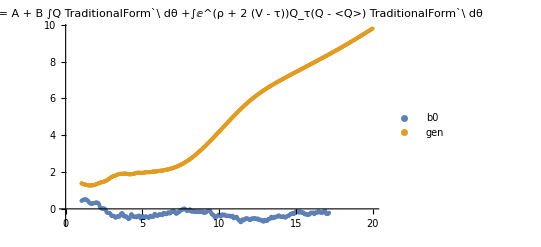
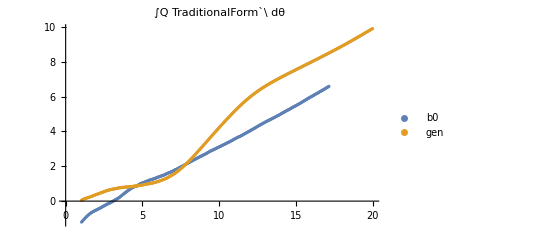
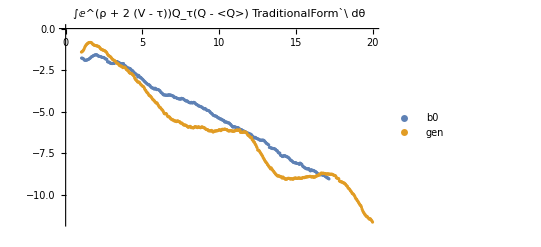
-Graphics- | -Graphics- | -Graphics-

```mathematica
p1={pairs["../long_runs/t_b0_89_4096.json",Log[Mean[Exp[ρ[#]]Vtau[#]]] & ]
,pairs["../long_runs/t_gen_24_4096.json",Log[Mean[Exp[ρ[#]]Vtau[#]]] & ]}//Map[Re[MovingAverage[#,50]]&]//ListPlot[#,PlotLegends->{"b0","gen"},PlotLabel->"∫ⅇ^ρ V = A + B ∫Q TraditionalForm`\ dθ +∫ⅇ^(ρ + 2 (V - τ))Q_τ(Q - <Q>) TraditionalForm`\ dθ",ImageSize->Scaled[1/3]]&;

p2={pairs["../long_runs/t_b0_89_4096.json",Log[Abs[Mean[q[#]]]] & ]
,pairs["../long_runs/t_gen_24_4096.json",Log[Abs[Mean[q[#]]]] & ]}//Map[Re[MovingAverage[#,50]]&]//ListPlot[#,PlotLegends->{"b0","gen"},PlotLabel->"∫Q TraditionalForm`\ dθ",ImageSize->Scaled[1/3]]&;

p3={pairs["../long_runs/t_b0_89_4096.json",Log[Mean[Exp[2(v[#]-τ[#])]Qtau[#](q[#]-Mean[q[#]])]] & ]
,pairs["../long_runs/t_gen_24_4096.json",Log[Mean[Exp[2(v[#]-τ[#])]Qtau[#](q[#]-Mean[q[#]])]] & ]}//Map[Re[MovingAverage[#,50]]&]//ListPlot[#,PlotLegends->{"b0","gen"},PlotLabel->"∫ⅇ^(ρ + 2 (V - τ))Q_τ(Q - <Q>) TraditionalForm`\ dθ",ImageSize->Scaled[1/3]]&;

Export["p1.svg",p1];
Export["p2.svg",p2];
Export["p3.svg",p3];
Export["p1.png",p1];
Export["p2.png",p2];
Export["p3.png",p3];

{{p1,p2,p3}}//TableForm
```

## Identifying corrupted files.

We have a problem with some of the simulation outputs being unreadable by Mathematica. We’d like to identify which ones those are, so we can resimulate them, or otherwise figure out what is wrong.

```mathematica
ParallelTable[
PrintTemporary[file];
Catch[
myimport[file];
Nothing
,file]
,{file,FileNames["*.json","../long_runs"]}
,Method->"FinestGrained"]
```

{}

Okay that didn’t produce any errors. Let’s now try to evaluate something along each file.

232

{b0_0_1024,b0_0_2048,b0_0_4096,b0_0_512,gen_0_1024,gen_0_2048,gen_0_4096,gen_0_512,b0_9_512,b0_13_512,b0_9_1024,b0_24_512,b0_13_1024,b0_26_512,b0_9_2048,b0_43_512,b0_24_1024,b0_13_2048,b0_26_1024,b0_58_512,b0_61_512,b0_64_512,b0_9_4096,b0_81_512,b0_85_512,b0_43_1024,b0_89_512,b0_24_2048,b0_13_4096,b0_26_2048,b0_58_1024,b0_121_512,b0_61_1024,b0_64_1024,b0_139_512,b0_162_512,b0_81_1024,b0_85_1024,b0_172_512,b0_43_2048,b0_89_1024,b0_179_512,b0_180_512,b0_190_512,b0_24_4096,b0_26_4096,b0_58_2048,b0_121_1024,b0_61_2048,b0_64_2048,b0_139_1024,b0_162_1024,b0_81_2048,b0_85_2048,b0_172_1024,b0_43_4096,b0_89_2048,b0_179_1024,b0_180_1024,b0_190_1024,b0_58_4096,b0_121_2048,b0_61_4096,b0_64_4096,b0_139_2048,b0_162_2048,b0_81_4096,b0_85_4096,b0_172_2048,b0_89_4096,b0_179_2048,b0_180_2048,b0_190_2048,b0_121_4096,b0_139_4096,b0_162_4096,b0_172_4096,b0_179_4096,b0_180_4096,b0_190_4096,gen_9_512,gen_13_512,gen_9_1024,gen_24_512,gen_13_1024,gen_9_2048,gen_43_512,gen_24_1024,gen_13_2048,gen_58_512,gen_61_512,gen_64_512,gen_69_512,gen_9_4096,gen_81_512,gen_85_512,gen_43_1024,gen_90_512,gen_24_2048,gen_13_4096,gen_58_1024,gen_121_512,gen_61_1024,gen_64_1024,gen_69_1024,gen_139_512,gen_156_512,gen_162_512,gen_81_1024,gen_163_512,gen_85_1024,gen_172_512,gen_43_2048,gen_179_512,gen_90_1024,gen_190_512,gen_192_512,gen_24_4096,gen_58_2048,gen_121_1024,gen_61_2048,gen_64_2048,gen_69_2048,gen_139_1024,gen_156_1024,gen_162_1024,gen_81_2048,gen_163_1024,gen_85_2048,gen_172_1024,gen_43_4096,gen_179_1024,gen_90_2048,gen_190_1024,gen_192_1024,gen_58_4096,gen_121_2048,gen_61_4096,gen_64_4096,gen_69_4096,gen_139_2048,gen_156_2048,gen_162_2048,gen_81_4096,gen_163_2048,gen_85_4096,gen_172_2048,gen_179_2048,gen_90_4096,gen_190_2048,gen_192_2048,gen_121_4096,gen_139_4096,gen_156_4096,gen_162_4096,gen_163_4096,gen_172_4096,gen_179_4096,gen_190_4096,gen_192_4096,pol_3_512,pol_3_1024,pol_3_2048,pol_3_4096,pol_90_512,pol_104_512,pol_105_512,pol_107_512,pol_108_512,pol_113_512,pol_124_512,pol_131_512,pol_144_512,pol_151_512,pol_164_512,pol_167_512,pol_168_512,pol_90_1024,pol_186_512,pol_193_512,pol_196_512,pol_197_512,pol_104_1024,pol_105_1024,pol_107_1024,pol_108_1024,pol_113_1024,pol_124_1024,pol_131_1024,pol_144_1024,pol_151_1024,pol_164_1024,pol_167_1024,pol_168_1024,pol_90_2048,pol_186_1024,pol_193_1024,pol_196_1024,pol_197_1024,pol_104_2048,pol_105_2048,pol_107_2048,pol_108_2048,pol_113_2048,pol_124_2048,pol_131_2048,pol_144_2048,pol_151_2048,pol_164_2048,pol_167_2048,pol_168_2048,pol_90_4096,pol_186_2048,pol_193_2048,pol_196_2048,pol_197_2048,pol_104_4096,pol_105_4096,pol_107_4096,pol_108_4096,pol_113_4096,pol_124_4096,pol_131_4096,pol_144_4096,pol_151_4096,pol_164_4096,pol_167_4096,pol_168_4096,pol_186_4096,pol_193_4096,pol_196_4096,pol_197_4096}

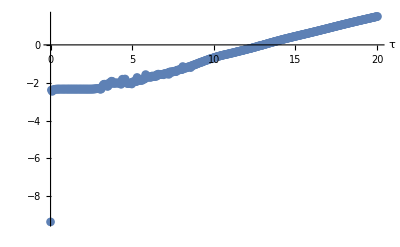
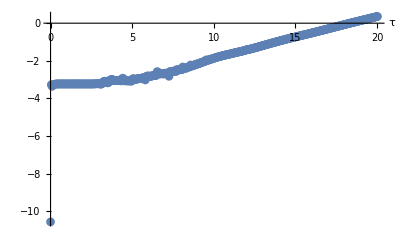
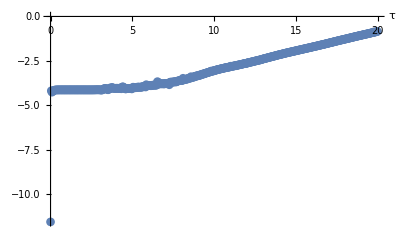
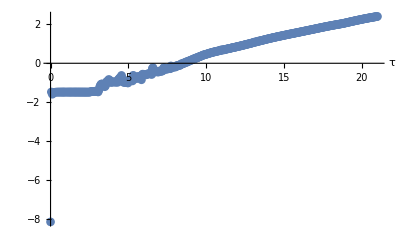
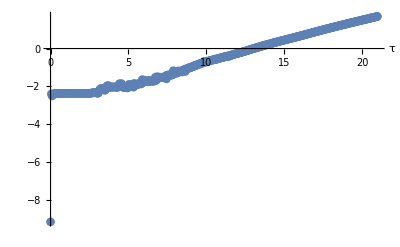
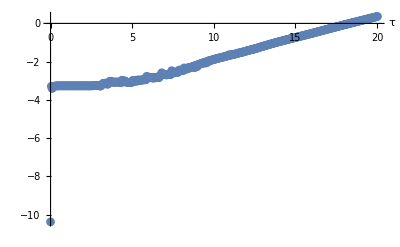
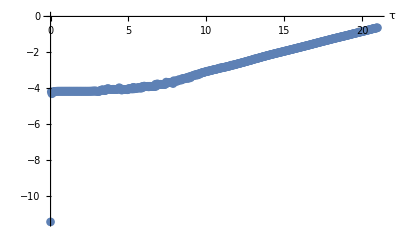
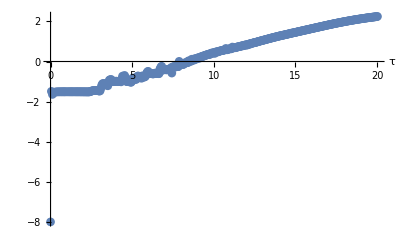
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |  |

```mathematica
Module[{type,filenames,runs,filess,k,print,i,dir,twidth},
dir="../long_runs/";
twidth=5;
filenames=FileNames["*t_*.1.json",{dir}];
i=0;
runs=filenames//StringReplace[dir<>"t_"~~typeandnumandres__~~"."~~__~~".json"->typeandnumandres]//Union//SortBy[ToExpression[#]&]//#[[;;]]&;
Print[runs//Length];
Print[runs];
Module[{tmp},
tmp=
Monitor[
Table[  (* For each run... *)
{
filee
,pairs[  (* ... get all the data from all the files ... *)
dir<>"t_"<>filee<>".json"
,{
galconstraint/*Abs/*Max/*Log10
,1/Π[#]Mean[Exp[ρ[#]]Ev[#]]&
,1/Π[#]Mean[Exp[ρ[#]]Eq[#]]&
,Mean[(l[#]-Log[1/2])]Exp[τ[#]/4]&
,Mean[(ρ[#]-τ[#]/2)Exp[ρ[#]]]/Mean[Exp[ρ[#]]]&
}[[1]] (* ... and apply the function I select from this little list ... *)
]//ListPlot[  (* ... then plot it ... *)
#
,PlotRange->{All,All}
,PlotStyle->PointSize[1/64]
,ImageSize->Scaled[1/twidth ]
,Epilog->Inset[Framed[filee,Background->LightYellow],ImageScaled[{.8,.2}]] (* ... with a nice label of the name of the run ... *)
,AxesLabel->{"τ",""}
]&
}
,{filee,runs}
]
,{ProgressIndicator[FirstPosition[runs,filee][[1]]-1,{0,runs//Length},ImageSize->Scaled[1/2]],filee}];(*
tmp//Map[Export[#[[1]]<>"_rho.png",#[[2]],ImageSize->1000]&];*) (* uncomment the stuff to the left if you'd like to write images of the plots to the disk. *)
tmp//Map[#[[2]]&]
]//Partition[#,UpTo[twidth]]&//TableForm (* ... and make a nice grid of all the plots for the runs. *)
]

Module[{path="pairs.mx"},
DumpSave[path,pairshelper2];
]
```

Also no problems here. Hm.